```mathematica
SetDirectory[NotebookDirectory[]];
```

6027

Hyper complex value = 1.00004+/-0.000284871

κ value = 0.00182138+/-0.00349472

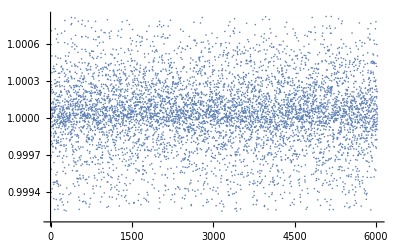

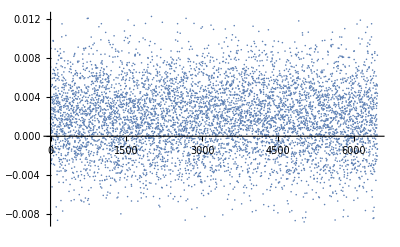

```mathematica
dataOct11F=Import["Oct11_data_fvals_2023.csv","Data"];
dataOct11k=Import["Oct11_data_kvals1_2023.csv","Data"];
Length[Flatten@dataOct11F]

Print["Hyper complex value = " ,Mean[Flatten@dataOct11F],"+/-",StandardDeviation[Flatten@dataOct11F]]
Print["κ value = " ,Mean[Flatten@dataOct11k],"+/-",StandardDeviation[Flatten@dataOct11k]]
ListPlot[dataOct11F]
ListPlot[dataOct11k]
```

```mathematica
Dimensions[Flatten@dataOct11F]
```

(6027)

```mathematica
DistributionFitTest[Flatten@dataOct11F,NormalDistribution[Mean[Flatten@dataOct11F],StandardDeviation[Flatten@dataOct11F]]]
DistributionFitTest[Flatten@dataOct11k,NormalDistribution[Mean[Flatten@dataOct11k],StandardDeviation[Flatten@dataOct11k]]]
```

3.75255×10^-14

0.70612

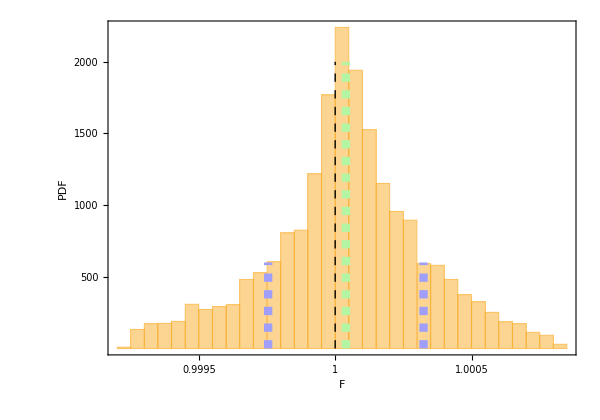

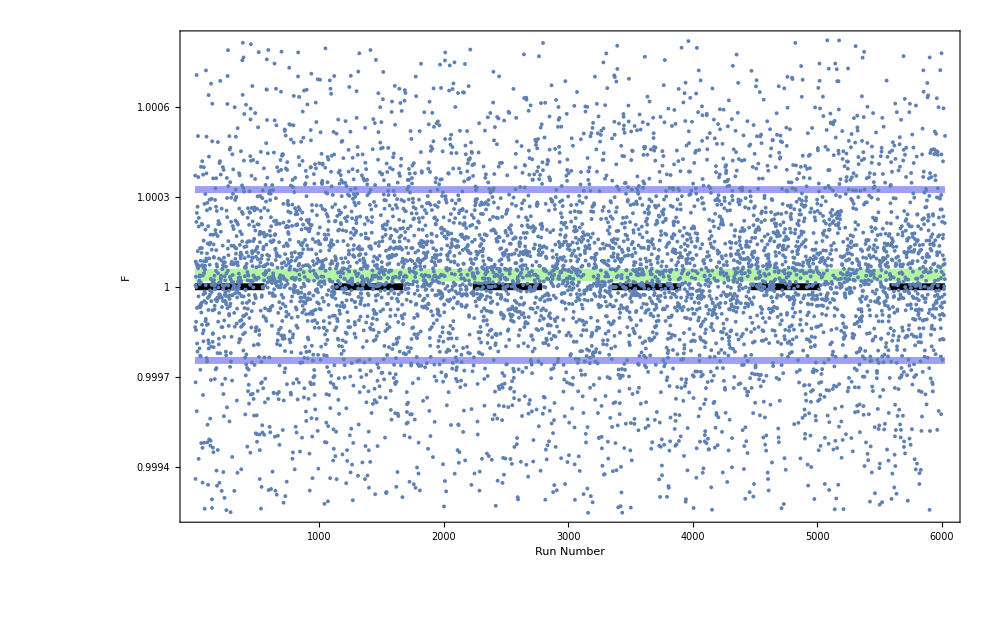

```mathematica
(*plotting one individual run*)
green=RGBColor[180/256,246/256,164/256];
square=Graphics[{Rectangle[{0,0}]}];
blueA=RGBColor[160/256,160/256,250/256];
Greenn=RGBColor[0/256,196/256,0/256];
Greenn2=RGBColor[108/258,195/256,250/256];
red=RGBColor[248/256,152/256,164/256];
x=0.002;
pdata=ListPlot[dataOct11F,Frame->False,Axes->False,PlotRange->{1-x,1+x}];
md=Mean[Flatten@dataOct11F];
sd=StandardDeviation[Flatten@dataOct11F];

ymax=2000;
ymax2=600;
plines=Plot[{md,md+sd,md-sd,1},{x,0,6027},PlotRange->All,Frame-> True,Frame-> Black,FrameLabel->{"Run Number","F"},FrameTicks->{{{0.9991,0.9994,0.9997,1,1.0003,1.0006},{None}},{{1000,2000,3000,4000,5000,6000},{None}}},LabelStyle->{FontFamily-> "CMU serif",34,Black},ImageSize->1000,PlotStyle->{{Thickness[0.009],green},{Thickness[0.005],blueA},{Thickness[0.005],blueA},{Thickness[0.005],Black,Dashing[0.05]}},PlotRange->{1-x,1+x},Axes->False];

pdf=PDF[NormalDistribution[md,sd]];
fs=36;

(*Plot[pdf[x],{x,0.999,1.001},PlotStyle->Directive[Thickness[0.01],Red]]*)
Show[Histogram[dataOct11F,30,"PDF"],Graphics[{Black,Thick,Dashing[0.01],Line[{{1,0},{1,ymax}}]}],Graphics[{green,Thickness[0.01],Dashing[0.01],Line[{{md,0},{md,ymax}}]}],Graphics[{blueA,Thickness[0.01],Dashing[0.01],Line[{{md+sd,0},{md+sd,ymax2}}]}],Graphics[{blueA,Thickness[0.01],Dashing[0.01],Line[{{md-sd,0},{md-sd,ymax2}}]}],ImageSize->600,AspectRatio->0.7,Frame-> True,FrameLabel->{"F","PDF"},FrameTicks->{{{500,1500,1000,2000},{None}},{{0.9995,1,1.0005},{None}}},LabelStyle->{FontFamily-> "CMU serif",fs,Black},ImageSize->1000,AspectRatio->0.5,FrameStyle->Directive[Black,Thickness[0.002]]]

Show[plines,pdata,FrameStyle->Directive[Black,Thickness[0.002]]]
```

{1,6462}

6462

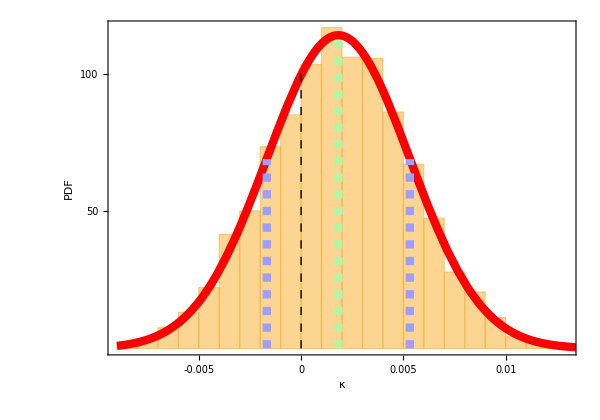

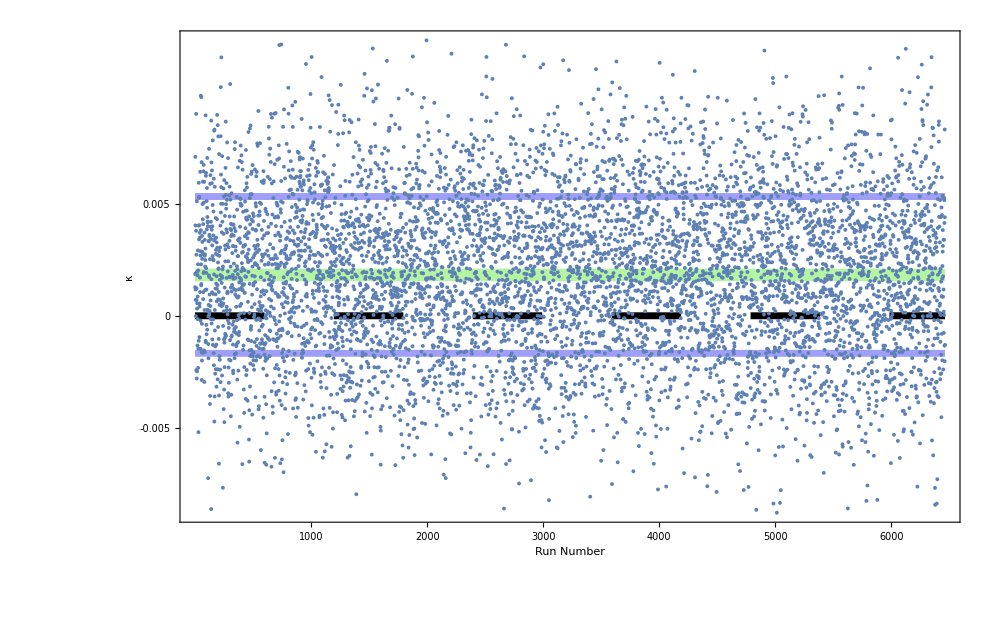

```mathematica
(*plotting one individual run*)
Dimensions[dataOct11k]
pdata=ListPlot[dataOct11k,Frame->False,Axes->False,PlotRange->{-x,x}];
md=Mean[Flatten@dataOct11k];
sd=StandardDeviation[Flatten@dataOct11k];

ymax=2000;
ymax2=600;
fs=30;
plines=Plot[{md,md+sd,md-sd,0},{x,0,6462},PlotRange->All,Frame-> True,Frame-> Black,FrameLabel->{"Run Number","κ"},FrameTicks->{{{-0.005,0,0.005},{None}},{{1000,2000,3000,4000,5000,6000},{None}}},LabelStyle->{FontFamily-> "CMU serif",fs,Black},ImageSize->1000,PlotStyle->{{Thickness[0.009],green},{Thickness[0.005],blueA},{Thickness[0.005],blueA},{Thickness[0.005],Black,Dashing[0.05]}},PlotRange->{-x,x},Axes->False];

pdf=PDF[NormalDistribution[md,sd]];


Length[Flatten@dataOct11k]
ymax=115;
ymax2=69;
Show[Histogram[dataOct11k,20,"PDF"],Plot[pdf[x],{x,-0.009,0.015},PlotStyle->Directive[Thickness[0.01],Red]],Graphics[{Black,Thick,Dashing[0.01],Line[{{0,0},{0,ymax*0.88}}]}],Graphics[{green,Thickness[0.01],Dashing[0.01],Line[{{md,0},{md,ymax}}]}],Graphics[{blueA,Thickness[0.01],Dashing[0.01],Line[{{md+sd,0},{md+sd,ymax2}}]}],Graphics[{blueA,Thickness[0.01],Dashing[0.01],Line[{{md-sd,0},{md-sd,ymax2}}]}],ImageSize->600,AspectRatio->0.7,Frame-> True,FrameLabel->{"κ","PDF"},FrameTicks->{{{100,200,50,2000},{None}},{{-0.01,-0.005,0,0.005,0.01},{None}}},LabelStyle->{FontFamily-> "CMU serif",fs,Black},ImageSize->1000,AspectRatio->0.5,FrameStyle->Directive[Black,Thickness[0.002]]]

Show[plines,pdata,FrameStyle->Directive[Black,Thickness[0.002]]]
```

```mathematica
dataOct11G123=Import["Oct11_data_G123vals.csv","Data"];
dataOct11G12=Import["Oct11_data_G12vals.csv","Data"];
dataOct11G13=Import["Oct11_data_G13vals.csv","Data"];
dataOct11G23=Import["Oct11_data_G23vals.csv","Data"];

Length[Flatten@dataOct11G123]

Print["G_123 value = " ,Mean[Flatten@dataOct11G123],"+/-",StandardDeviation[Flatten@dataOct11G123]]
Print["G_12 value = " ,Mean[Flatten@dataOct11G12],"+/-",StandardDeviation[Flatten@dataOct11G12]]
Print["G_13 value = " ,Mean[Flatten@dataOct11G13],"+/-",StandardDeviation[Flatten@dataOct11G13]]
Print["G_23 value = " ,Mean[Flatten@dataOct11G23],"+/-",StandardDeviation[Flatten@dataOct11G23]]
```

6471

G_123 value = 0.00249008+/-0.00251173

G_12 value = -0.000983429+/-0.0026277

G_13 value = -0.000210598+/-0.00263447

G_23 value = -0.000744626+/-0.00264804

```mathematica
DistributionFitTest[Flatten@dataOct11G123,NormalDistribution[Mean[Flatten@dataOct11G123],StandardDeviation[Flatten@dataOct11G123]]]
DistributionFitTest[Flatten@dataOct11G12,NormalDistribution[Mean[Flatten@dataOct11G12],StandardDeviation[Flatten@dataOct11G12]]]
DistributionFitTest[Flatten@dataOct11G13,NormalDistribution[Mean[Flatten@dataOct11G13],StandardDeviation[Flatten@dataOct11G13]]]
DistributionFitTest[Flatten@dataOct11G23,NormalDistribution[Mean[Flatten@dataOct11G23],StandardDeviation[Flatten@dataOct11G23]]]
```

0.652801

0.797497

0.897987

0.979341

```mathematica
Length[Flatten@dataOct11G12]
Length[Flatten@dataOct11G13]
Length[Flatten@dataOct11G23]
Length[Flatten@dataOct11G123]
```

6464

6465

6477

6471

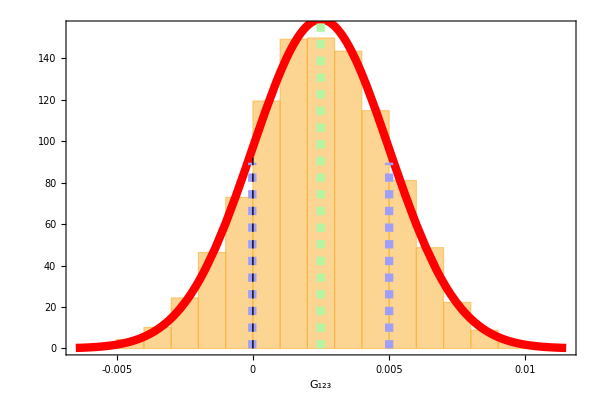

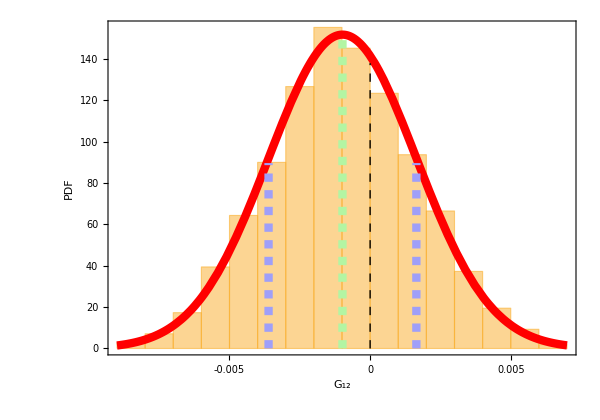

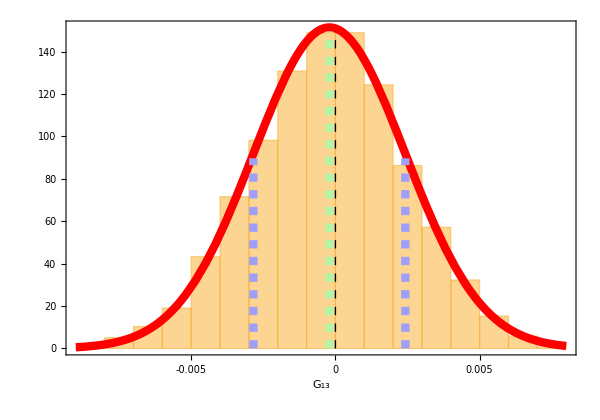

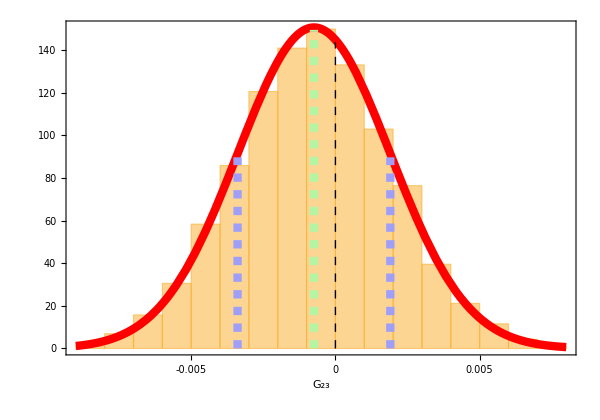

```mathematica
ymax=115;
ymax2=69;

md=Mean[Flatten@dataOct11G123];
sd=StandardDeviation[Flatten@dataOct11G123];

pdf=PDF[NormalDistribution[md,sd]];
Show[Histogram[dataOct11G123,20,"PDF"],Plot[pdf[x],{x,-0.0065,0.0115},PlotStyle->Directive[Thickness[0.01],Red]],Graphics[{green,Thickness[0.01],Dashing[0.01],Line[{{md,0},{md,ymax*1.38}}]}],Graphics[{blueA,Thickness[0.01],Dashing[0.01],Line[{{md+sd,0},{md+sd,ymax2*1.3}}]}],Graphics[{blueA,Thickness[0.01],Dashing[0.01],Line[{{md-sd,0},{md-sd,ymax2*1.3}}]}],Graphics[{Black,Thick,Dashing[0.01],Line[{{0,0},{0,ymax*0.8}}]}],ImageSize->600,AspectRatio->0.7,Frame-> True,FrameLabel->{"G_123",""},FrameTicks->{{{None},{None}},{{-0.01,-0.005,0,0.005,0.01},{None}}},LabelStyle->{FontFamily-> "CMU serif",fs,Black},ImageSize->1000,AspectRatio->0.5,FrameStyle->Directive[Black,Thickness[0.002]],PlotRange->{{-0.0065,0.0115},{0,155}}]

md=Mean[Flatten@dataOct11G12];
sd=StandardDeviation[Flatten@dataOct11G12];

pdf=PDF[NormalDistribution[md,sd]];
Show[Histogram[dataOct11G12,20,"PDF"],Plot[pdf[x],{x,-0.009,0.007},PlotStyle->Directive[Thickness[0.01],Red]],Graphics[{green,Thickness[0.01],Dashing[0.01],Line[{{md,0},{md,ymax*1.3}}]}],Graphics[{blueA,Thickness[0.01],Dashing[0.01],Line[{{md+sd,0},{md+sd,ymax2*1.3}}]}],Graphics[{blueA,Thickness[0.01],Dashing[0.01],Line[{{md-sd,0},{md-sd,ymax2*1.3}}]}],Graphics[{Black,Thick,Dashing[0.01],Line[{{0,0},{0,ymax*1.2}}]}],ImageSize->600,AspectRatio->0.7,Frame-> True,FrameLabel->{"G_12","PDF"},FrameTicks->{{{},{None}},{{-0.01,-0.005,0,0.005,0.01},{None}}},LabelStyle->{FontFamily-> "CMU serif",fs,Black},ImageSize->1000,AspectRatio->0.5,FrameStyle->Directive[Black,Thickness[0.002]]]


md=Mean[Flatten@dataOct11G13];
sd=StandardDeviation[Flatten@dataOct11G13];

pdf=PDF[NormalDistribution[md,sd]];
Show[Histogram[dataOct11G13,20,"PDF"],Plot[pdf[x],{x,-0.009,0.008},PlotStyle->Directive[Thickness[0.01],Red]],Graphics[{Black,Thick,Dashing[0.01],Line[{{0,0},{0,ymax*1.3}}]}],Graphics[{green,Thickness[0.01],Dashing[0.01],Line[{{md,0},{md,ymax*1.3}}]}],Graphics[{blueA,Thickness[0.01],Dashing[0.01],Line[{{md+sd,0},{md+sd,ymax2*1.3}}]}],Graphics[{blueA,Thickness[0.01],Dashing[0.01],Line[{{md-sd,0},{md-sd,ymax2*1.3}}]}],ImageSize->600,AspectRatio->0.7,Frame-> True,FrameLabel->{"G_13",""},FrameTicks->{{{},{None}},{{-0.01,-0.005,0,0.005,0.01},{None}}},LabelStyle->{FontFamily-> "CMU serif",fs,Black},ImageSize->1000,AspectRatio->0.5,FrameStyle->Directive[Black,Thickness[0.002]]]

md=Mean[Flatten@dataOct11G23];
sd=StandardDeviation[Flatten@dataOct11G23];

pdf=PDF[NormalDistribution[md,sd]];
Show[Histogram[dataOct11G23,20,"PDF"],Plot[pdf[x],{x,-0.009,0.008},PlotStyle->Directive[Thickness[0.01],Red]],Graphics[{Black,Thick,Dashing[0.01],Line[{{0,0},{0,ymax*1.25}}]}],Graphics[{green,Thickness[0.01],Dashing[0.01],Line[{{md,0},{md,ymax*1.3}}]}],Graphics[{blueA,Thickness[0.01],Dashing[0.01],Line[{{md+sd,0},{md+sd,ymax2*1.3}}]}],Graphics[{blueA,Thickness[0.01],Dashing[0.01],Line[{{md-sd,0},{md-sd,ymax2*1.3}}]}],ImageSize->600,AspectRatio->0.7,Frame-> True,FrameLabel->{"G_23",""},FrameTicks->{{{},{None}},{{-0.01,-0.005,0,0.005,0.01},{None}}},LabelStyle->{FontFamily-> "CMU serif",fs,Black},ImageSize->1000,AspectRatio->0.5,FrameStyle->Directive[Black,Thickness[0.002]]]
```